```mathematica
Clear["Global`*"]

(*THIS SECTION IS TO IMPORT THE FILES ON MAC OS*)

data1 = Import["/Users/rodolfoaguirre/Desktop/Sigma7-111_BothGBs/E0.75/BothGBs_05ns_T_1600.txt","Table"];
data2 = Import["/Users/rodolfoaguirre/Desktop/Sigma7-111_BothGBs/E0.75/BothGBs_05ns_T_1700.txt","Table"];
data3 = Import["/Users/rodolfoaguirre/Desktop/Sigma7-111_BothGBs/E0.75/BothGBs_05ns_T_1800.txt","Table"];
data4 = Import["/Users/rodolfoaguirre/Desktop/Sigma7-111_BothGBs/E0.75/BothGBs_05ns_T_1900.txt","Table"];
data5 = Import["/Users/rodolfoaguirre/Desktop/Sigma7-111_BothGBs/E0.75/BothGBs_05ns_T_2000.txt","Table"];

data6 = Import["/Users/rodolfoaguirre/Desktop/Sigma7-111_BothGBs/E1.0/BothGBs_05ns_T_1600.txt","Table"];
data7 = Import["/Users/rodolfoaguirre/Desktop/Sigma7-111_BothGBs/E1.0/BothGBs_05ns_T_1700.txt","Table"];
data8 = Import["/Users/rodolfoaguirre/Desktop/Sigma7-111_BothGBs/E1.0/BothGBs_05ns_T_1800.txt","Table"];
data9 = Import["/Users/rodolfoaguirre/Desktop/Sigma7-111_BothGBs/E1.0/BothGBs_05ns_T_1900.txt","Table"];
data10 = Import["/Users/rodolfoaguirre/Desktop/Sigma7-111_BothGBs/E1.0/BothGBs_05ns_T_2000.txt","Table"];

data11 = Import["/Users/rodolfoaguirre/Desktop/Sigma7-111_BothGBs/E1.25/BothGBs_05ns_T_1600.txt","Table"];
data12 = Import["/Users/rodolfoaguirre/Desktop/Sigma7-111_BothGBs/E1.25/BothGBs_05ns_T_1700.txt","Table"];
data13 = Import["/Users/rodolfoaguirre/Desktop/Sigma7-111_BothGBs/E1.25/BothGBs_05ns_T_1800.txt","Table"];
data14 = Import["/Users/rodolfoaguirre/Desktop/Sigma7-111_BothGBs/E1.25/BothGBs_05ns_T_1900.txt","Table"];
data15 = Import["/Users/rodolfoaguirre/Desktop/Sigma7-111_BothGBs/E1.25/BothGBs_05ns_T_2000.txt","Table"];
```

```mathematica
d1=∑_(n=1)^51 (a×data1[[n,1]] - a/b+ A/b Exp[(-Ea + c×0.75)/0.137] - A/b Exp[(-Ea+c×0.75)/0.137-b×data1[[n,1]]]+a/b Exp[-b×data1[[n,1]]]-data1[[n,2]])^2;
d2=∑_(n=1)^51 (a×data2[[n,1]] - a/b+ A/b Exp[(-Ea + c×0.75)/0.146] - A/b Exp[(-Ea+c×0.75)/0.146-b×data2[[n,1]]]+a/b Exp[-b×data2[[n,1]]]-data2[[n,2]])^2;
d3=∑_(n=1)^51 (a×data3[[n,1]] - a/b+ A/b Exp[(-Ea + c×0.75)/0.155] - A/b Exp[(-Ea+c×0.75)/0.155-b×data3[[n,1]]]+a/b Exp[-b×data3[[n,1]]]-data3[[n,2]])^2;
d4=∑_(n=1)^51 (a×data4[[n,1]] - a/b+ A/b Exp[(-Ea + c×0.75)/0.163] - A/b Exp[(-Ea+c×0.75)/0.163-b×data4[[n,1]]]+a/b Exp[-b×data4[[n,1]]]-data4[[n,2]])^2;
d5=∑_(n=1)^51 (a×data5[[n,1]] - a/b+ A/b Exp[(-Ea + c×0.75)/0.172] - A/b Exp[(-Ea+c×0.75)/0.172-b×data5[[n,1]]]+a/b Exp[-b×data5[[n,1]]]-data5[[n,2]])^2;

d6=∑_(n=1)^51 (a×data6[[n,1]] - a/b+ A/b Exp[(-Ea + c×1.0)/0.137] - A/b Exp[(-Ea+c×1.0)/0.137-b×data6[[n,1]]]+a/b Exp[-b×data6[[n,1]]]-data6[[n,2]])^2;
d7=∑_(n=1)^51 (a×data7[[n,1]] - a/b+ A/b Exp[(-Ea + c×1.0)/0.146] - A/b Exp[(-Ea+c×1.0)/0.146-b×data7[[n,1]]]+a/b Exp[-b×data7[[n,1]]]-data7[[n,2]])^2;
d8=∑_(n=1)^51 (a×data8[[n,1]] - a/b+ A/b Exp[(-Ea + c×1.0)/0.155] - A/b Exp[(-Ea+c×1.0)/0.155-b×data8[[n,1]]]+a/b Exp[-b×data8[[n,1]]]-data8[[n,2]])^2;
d9=∑_(n=1)^51 (a×data9[[n,1]] - a/b+ A/b Exp[(-Ea + c×1.0)/0.163] - A/b Exp[(-Ea+c×1.0)/0.163-b×data9[[n,1]]]+a/b Exp[-b×data9[[n,1]]]-data9[[n,2]])^2;
d10=∑_(n=1)^51 (a×data10[[n,1]] - a/b+ A/b Exp[(-Ea+ c×1.0)/0.172] - A/b Exp[(-Ea+c×1.0)/0.172-b×data10[[n,1]]]+a/b Exp[-b×data10[[n,1]]]-data10[[n,2]])^2;

d11=∑_(n=1)^51 (a×data11[[n,1]] - a/b+ A/b Exp[(-Ea + c×1.25)/0.137] - A/b Exp[(-Ea+c×1.25)/0.137-b×data11[[n,1]]]+a/b Exp[-b×data11[[n,1]]]-data11[[n,2]])^2;
d12=∑_(n=1)^51 (a×data12[[n,1]] - a/b+ A/b Exp[(-Ea + c×1.25)/0.146] - A/b Exp[(-Ea+c×1.25)/0.146-b×data12[[n,1]]]+a/b Exp[-b×data12[[n,1]]]-data12[[n,2]])^2;
d13=∑_(n=1)^51 (a×data13[[n,1]] - a/b+ A/b Exp[(-Ea + c×1.25)/0.155] - A/b Exp[(-Ea+c×1.25)/0.155-b×data13[[n,1]]]+a/b Exp[-b×data13[[n,1]]]-data13[[n,2]])^2;
d14=∑_(n=1)^51 (a×data14[[n,1]] - a/b+ A/b Exp[(-Ea + c×1.25)/0.163] - A/b Exp[(-Ea+c×1.25)/0.163-b×data14[[n,1]]]+a/b Exp[-b×data14[[n,1]]]-data14[[n,2]])^2;
d15=∑_(n=1)^51 (a×data15[[n,1]] - a/b+ A/b Exp[(-Ea+ c×1.25)/0.172] - A/b Exp[(-Ea+c×1.25)/0.172-b×data15[[n,1]]]+a/b Exp[-b×data15[[n,1]]]-data15[[n,2]])^2;



e1=∑_(n=1)^51 (a×data1[[n,1]] - a/b+ A/b Exp[(-Ea + c×0.75)/0.137] - A/b Exp[(-Ea+c×0.75)/0.137-b×data1[[n,1]]]+a/b Exp[-b×data1[[n,1]]]-data1[[n,3]])^2;
e2=∑_(n=1)^51 (a×data2[[n,1]] - a/b+ A/b Exp[(-Ea + c×0.75)/0.146] - A/b Exp[(-Ea+c×0.75)/0.146-b×data2[[n,1]]]+a/b Exp[-b×data2[[n,1]]]-data2[[n,3]])^2;
e3=∑_(n=1)^51 (a×data3[[n,1]] - a/b+ A/b Exp[(-Ea + c×0.75)/0.155] - A/b Exp[(-Ea+c×0.75)/0.155-b×data3[[n,1]]]+a/b Exp[-b×data3[[n,1]]]-data3[[n,3]])^2;
e4=∑_(n=1)^51 (a×data4[[n,1]] - a/b+ A/b Exp[(-Ea + c×0.75)/0.163] - A/b Exp[(-Ea+c×0.75)/0.163-b×data4[[n,1]]]+a/b Exp[-b×data4[[n,1]]]-data4[[n,3]])^2;
e5=∑_(n=1)^51 (a×data5[[n,1]] - a/b+ A/b Exp[(-Ea + c×0.75)/0.172] - A/b Exp[(-Ea+c×0.75)/0.172-b×data5[[n,1]]]+a/b Exp[-b×data5[[n,1]]]-data5[[n,3]])^2;

e6=∑_(n=1)^51 (a×data6[[n,1]] - a/b+ A/b Exp[(-Ea + c×1.0)/0.137] - A/b Exp[(-Ea+c×1.0)/0.137-b×data6[[n,1]]]+a/b Exp[-b×data6[[n,1]]]-data6[[n,3]])^2;
e7=∑_(n=1)^51 (a×data7[[n,1]] - a/b+ A/b Exp[(-Ea + c×1.0)/0.146] - A/b Exp[(-Ea+c×1.0)/0.146-b×data7[[n,1]]]+a/b Exp[-b×data7[[n,1]]]-data7[[n,3]])^2;
e8=∑_(n=1)^51 (a×data8[[n,1]] - a/b+ A/b Exp[(-Ea + c×1.0)/0.155] - A/b Exp[(-Ea+c×1.0)/0.155-b×data8[[n,1]]]+a/b Exp[-b×data8[[n,1]]]-data8[[n,3]])^2;
e9=∑_(n=1)^51 (a×data9[[n,1]] - a/b+ A/b Exp[(-Ea + c×1.0)/0.163] - A/b Exp[(-Ea+c×1.0)/0.163-b×data9[[n,1]]]+a/b Exp[-b×data9[[n,1]]]-data9[[n,3]])^2;
e10=∑_(n=1)^51 (a×data10[[n,1]] - a/b+ A/b Exp[(-Ea+ c×1.0)/0.172] - A/b Exp[(-Ea+c×1.0)/0.172-b×data10[[n,1]]]+a/b Exp[-b×data10[[n,1]]]-data10[[n,3]])^2;

e11=∑_(n=1)^51 (a×data11[[n,1]] - a/b+ A/b Exp[(-Ea + c×1.25)/0.137] - A/b Exp[(-Ea+c×1.25)/0.137-b×data11[[n,1]]]+a/b Exp[-b×data11[[n,1]]]-data11[[n,3]])^2;
e12=∑_(n=1)^51 (a×data12[[n,1]] - a/b+ A/b Exp[(-Ea + c×1.25)/0.146] - A/b Exp[(-Ea+c×1.25)/0.146-b×data12[[n,1]]]+a/b Exp[-b×data12[[n,1]]]-data12[[n,3]])^2;
e13=∑_(n=1)^51 (a×data13[[n,1]] - a/b+ A/b Exp[(-Ea + c×1.25)/0.155] - A/b Exp[(-Ea+c×1.25)/0.155-b×data13[[n,1]]]+a/b Exp[-b×data13[[n,1]]]-data13[[n,3]])^2;
e14=∑_(n=1)^51 (a×data14[[n,1]] - a/b+ A/b Exp[(-Ea + c×1.25)/0.163] - A/b Exp[(-Ea+c×1.25)/0.163-b×data14[[n,1]]]+a/b Exp[-b×data14[[n,1]]]-data14[[n,3]])^2;
e15=∑_(n=1)^51 (a×data15[[n,1]] - a/b+ A/b Exp[(-Ea+ c×1.25)/0.172] - A/b Exp[(-Ea+c×1.25)/0.172-b×data15[[n,1]]]+a/b Exp[-b×data15[[n,1]]]-data15[[n,3]])^2;

dtotal = d1+d2+d3+d4+d5+d6+d7+d8+d9+d10+d11+d12+d13+d14+d15;
etotal = e1+e2+e3+e4+e5+e6+e7+e8+e9+e10+e11+e12+e13+e14+e15;
```

```mathematica
iteration1=10000;
randoms1=101;
toscreen1=
Timing[afm1=NMinimize[{dtotal,0.0001≤A,-2500.0≤a,0.0001≤b,0.0001≤c,0.0001≤Ea},{{A,3746.0,3747.000},{a,25.0,26.0},{b,12.0,14.0},{c,0.0001,1.0},{Ea,0.0001,1.0}},MaxIterations->iteration1,Method->{"SimulatedAnnealing","RandomSeed"->randoms1}]];
Print[toscreen1];
error=toscreen1[[2,1]];
pot=toscreen1[[2,2]];

iteration2=10000;
randoms2=101;
toscreen2=
Timing[afm2=NMinimize[{dtotal,0.0001≤A,-2500.0≤a,0.0001≤b,0.0001≤c,0.0001≤Ea},{{A,3746.0,3747.000},{a,25.0,26.0},{b,12.0,14.0},{c,0.0001,1.0},{Ea,0.0001,1.0}},MaxIterations->iteration2]];
Print[toscreen2];
If[error>toscreen2[[2,1]],
error=toscreen2[[2,1]];
pot=toscreen2[[2,2]];
];

iteration3=10000;
randoms3=1001;
toscreen3=
Timing[afm3=NMinimize[{dtotal,0.0001≤A,-2500.0≤a,0.0001≤b,0.0001≤c,0.0001≤Ea},{{A,3746.0,3747.000},{a,25.0,26.0},{b,12.0,14.0},{c,0.0001,1.0},{Ea,0.0001,1.0}},MaxIterations->iteration3,Method->{"NelderMead","RandomSeed"->randoms3}]];
Print[toscreen3];
If[error>toscreen3⟦2,1⟧,
error=toscreen3⟦2,1⟧;
pot=toscreen3⟦2,2⟧;
];
```

{100.788,{16824.3,{A→889.22,a→44.7631,b→7.52064,c→0.175291,Ea→0.243293}}}

{16.5747,{16824.3,{A→889.22,a→44.7636,b→7.52065,c→0.175291,Ea→0.243293}}}

{16.8432,{16824.3,{A→889.23,a→44.7719,b→7.5209,c→0.175293,Ea→0.243296}}}

```mathematica
iteration1=10000;
randoms1=101;
toscreen1=
Timing[afm1=NMinimize[{etotal,0.0001≤A,-2500.0≤a,0.0001≤b,0.0001≤c,0.0001≤Ea},{{A,3746.0,3747.000},{a,25.0,26.0},{b,12.0,14.0},{c,0.0001,1.0},{Ea,0.0001,1.0}},MaxIterations->iteration1,Method->{"SimulatedAnnealing","RandomSeed"->randoms1}]];
Print[toscreen1];
error=toscreen1[[2,1]];
pot=toscreen1[[2,2]];

iteration2=10000;
randoms2=101;
toscreen2=
Timing[afm2=NMinimize[{etotal,0.0001≤A,-2500.0≤a,0.0001≤b,0.0001≤c,0.0001≤Ea},{{A,3746.0,3747.000},{a,25.0,26.0},{b,12.0,14.0},{c,0.0001,1.0},{Ea,0.0001,1.0}},MaxIterations->iteration2]];
Print[toscreen2];
If[error>toscreen2[[2,1]],
error=toscreen2[[2,1]];
pot=toscreen2[[2,2]];
];

iteration3=10000;
randoms3=1001;
toscreen3=
Timing[afm3=NMinimize[{etotal,0.0001≤A,-2500.0≤a,0.0001≤b,0.0001≤c,0.0001≤Ea},{{A,3746.0,3747.000},{a,25.0,26.0},{b,12.0,14.0},{c,0.0001,1.0},{Ea,0.0001,1.0}},MaxIterations->iteration3,Method->{"NelderMead","RandomSeed"->randoms3}]];
Print[toscreen3];
If[error>toscreen3⟦2,1⟧,
error=toscreen3⟦2,1⟧;
pot=toscreen3⟦2,2⟧;
];
```

{57.0681,{11221.7,{A→5421.39,a→34.8394,b→16.519,c→0.1825,Ea→0.50083}}}

{6.15249,{11221.7,{A→5421.39,a→34.8394,b→16.519,c→0.1825,Ea→0.50083}}}

{6.88509,{11221.7,{A→5421.39,a→34.8394,b→16.519,c→0.1825,Ea→0.50083}}}

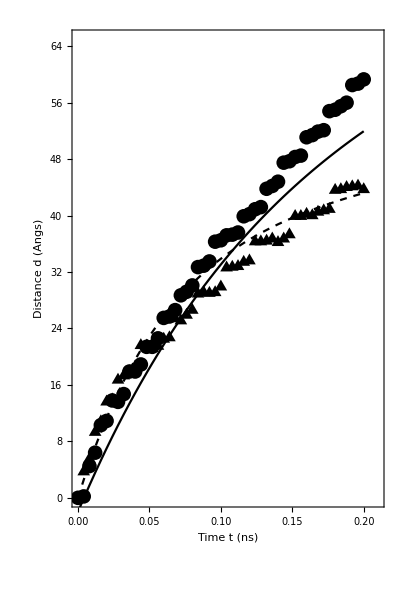

```mathematica
texp = data1[[Range[51],1]];
kT = (8.617×10^-5)×2000;
appE = 0.75;


A=5421.39;
a=34.8394;
b=16.519;
c=0.1825;
Ea=0.50083;

AA = 889.22;
aa = 44.7631;
bb = 7.520648;
cc = 0.175292;
Eaa=0.243292;

(*eva = 25.712×texp - 25.712/13.0875+ 3746.31/13.0875 Exp[(-0.445446+ 0.170398×appE)/kT] - 3746.31/13.0875 Exp[(-0.445446+0.170398×appE)/kT-13.0875×texp]+25.712/13.0875 Exp[-13.0875×texp];*)

eva1 = a×texp - a/b+ A/b Exp[(-Ea+ c×appE)/kT] - A/b Exp[(-Ea+c×appE)/kT-b×texp]+a/b Exp[-b×texp];
eva2 = aa×texp - aa/bb+ AA/bb Exp[(-Eaa+ cc×appE)/kT] - AA/bb Exp[(-Eaa+c×appE)/kT-bb×texp]+aa/bb Exp[-bb×texp];

fdata1= Transpose@{texp, eva1};
fdata2= Transpose@{texp, eva2};
GB1 = data5[[Range[51],2]];
GB2=data5[[Range[51],3]];
realdata1 = Transpose@{texp,GB1};
realdata2 = Transpose@{texp,GB2};

(*ListPlot[{fdata,data6[[1]]},AxesLabel->{"Time(ns)","Distance(A)"}, PlotRange->{{0,0.34},{0,57}}]*)
(*ListPlot[{fdata,data18[[1,Range[51]]]},AxesLabel->{"Time(ns)","Distance(A)"}]*)

(*Show[ListPlot[realdata1,AxesLabel->{"Time t (ns)","Distance d (Angs)"},PlotStyle->{Black}, PlotRange->{{0,0.21},{0,85}},BaseStyle->{FontWeight->"Bold",FontSize->30},PlotMarkers->{●,10},ImageSize->{600,700}],ListPlot[realdata2, PlotStyle->Black,PlotMarkers->{▲,10}],ListLinePlot[{fdata1,fdata2},PlotStyle->{Black,Black}]]*)


Show[ListPlot[realdata1,PlotStyle->{Black,Dashed}, PlotRange->{{0,0.21},{0,65}},BaseStyle->{FontWeight->"Bold",FontSize->25},PlotMarkers->{●,15},AspectRatio->1.5],ListPlot[realdata2, PlotStyle->Black,PlotMarkers->{▲,15}],ListLinePlot[{fdata1,fdata2},PlotStyle->{{Black,Dashed},Black}],Frame-> True, FrameLabel->{{"Distance d (Angs)",""},{"Time t (ns)",""}},LabelStyle->Directive[Black,20,FontFamily->"Helvetica"]]



(*ListLinePlot[{fdata2},PlotStyle->Thickness[0.005]],PlotStyle->Blue]*)

(*ListPlot[data1[[Range[51],2]]]*)

(*ListPlot[{testData1,testData2,testData3},PlotMarkers->{{●,10},{▲,10},{■,10}}]*)

(*,AxesLabel->{"Time(ns)","Distance(A)"},PlotRange->{{0,0.21},{0,85}}, PlotStyle->Purple, BaseStyle->{FontWeight->"Bold",FontSize->20},PlotMarkers->{Automatic,10}]*)
```